```mathematica
Remove["Global`*"];
ClearAll["Global`*"];
Tstar[ii_,x_]:=Simplify[ChebyshevT[ii,2x-1]];
𝒳[frist_,end_,t_]:=Piecewise[{{1,frist≤t && t≤end}},0];
TT[mm_,x_]:=Piecewise[{{1/(√π),mm==0},{√(2/π)ChebyshevT[mm,x],mm>0}},0];
ψ[nn_,mm_,X_]:=Module[{x=X},
Return[Piecewise[{{2^((k+1)/2)TT[mm,2^(k+1)x-(2nn+1)],  nn/2^k≤ x && x≤ (nn+1)/2^k }},0]];
];
γ[mm_]:=Piecewise[{{2,mm== 0},{1,mm≥ 1}}];
Ψ[x_]:=Flatten[Table[ψ[i,j,x],{i,0,2^k-1},{j,0,M}]];
a[mm_,ii_]:=If[mm==0 && ii== 0,1,(-1)^ii 2^(2mm-2ii)(mm(2mm-ii-1)!)/(ii! (2mm-2ii)!)];
caputo[f_,{xx_,αα_},var_]:=Module[{nn=Ceiling[αα]},
If[!IntegerQ[αα],
Return[1/Gamma[nn-αα] Integrate[D[f/.xx->τ,{τ,nn}]/(var-τ)^(αα-nn+1),{τ,0,var},Assumptions->var>0]];
,
Return[D[f,{xx,nn}]/.Indeterminate->0];
];
];
w[mm_,nn_,qq_,αα_]:=Module[{},
Return[Piecewise[{{∑_(i=0)^mm 2^(k(mm-i))b[αα,mm,mm-i,qq]a[mm,i],nn== 0}},∑_(i=0)^mm ∑_(j=0)^(mm-i) b[αα,mm,j,qq]a[mm,i]Binomial[mm-i,j](-1)^(mm-i-j)2^(k j)nn^(mm-i-j)]];
];
Dstar[αα_,tt_]:=Module[{},
DαΨ=Flatten[Table[,{i,0,2^k-1},{j,0,M}]];
n=0;
For[m=0,m≤M,m++,
kk=n(M+1)+m+1;
DαΨ⟦kk⟧= 2^((k+1)/2)√(2/(π γ[m]))∑_(i=0)^m 2^(k(m-i))a[m,i]caputo[t^(m-i)Piecewise[{{1,0≤ t && t≤  1/2^k}},0],{t,αα},t];
];
For[n=1,n≤2^k-1,n++,
For[m=0,m≤M,m++,
kk=n(M+1)+m+1;
DαΨ⟦kk⟧= 2^((k+1)/2)√(2/(π γ[m]))∑_(i=0)^m ∑_(j=0)^(m-i) a[m,i]Binomial[m-i,j](-1)^(m-i-j)2^(k j)n^(m-i-j)caputo[t^j Piecewise[{{1,n/2^k≤ t && t≤  (n+1)/2^k}},0],{t,αα},t];
];
];
Return[Simplify[DαΨ]];
];
g[t_]:=Module[{},
Return[{Simplify[caputo[yReal[t]⟦1⟧,{t,α⟦1⟧},t]-yReal[t]⟦2⟧-Integrate[(t-s)^(-1/2)(yReal[t]⟦1⟧+(yReal[t]⟦2⟧)^2),{s,0,t},Assumptions->t>0]],
Simplify[caputo[yReal[t]⟦2⟧,{t,α⟦2⟧},t]-(yReal[t]⟦1⟧)^3-Integrate[(t-s)^(-2/3)(yReal[t]⟦1⟧+yReal[t]⟦2⟧),{s,0,t},Assumptions->t>0]]
}
];
];

(**************************************)
α={3/4,1/2};
f[t_]={{0,1},{1,0}};
β={1/2,2/3};
K[t_,s_]={{1,0},{1,1}};
y0={0,0};
yReal[t_]={t^2,t^3};
k=1;M=4;
(*********************************)
lenghtα=Length[α];
c=Table[Subscript[CC, i ,j],{i,lenghtα},{j,2^k(M+1)}];
yt[t_]=Simplify[c.Ψ[t]];
Ans[t_]={Simplify[-(c⟦1⟧.Dstar[α⟦1⟧,t])+g[t]⟦1⟧+yt[t]⟦2⟧+Integrate[((t-s)^(-1/2)((yt[s])⟦1⟧+((yt[s])⟦2⟧)^2)),{s,0,t},Assumptions->t>0]],
Simplify[-(c⟦2⟧.Dstar[α⟦2⟧,t])+g[t]⟦2⟧+(yt[t]⟦1⟧)^3+Integrate[((t-s)^(-2/3)((yt[s])⟦1⟧+(yt[s])⟦2⟧)),{s,0,t},Assumptions->t>0]]
}
```

{-2 t^(5/2)-t^3-2 t^(13/2)+(32 t^(5/4))/(5 Gamma[1/4])+(Piecewise[{{(4 √t (765765 √π CC_(1,1)+255255 √(2 π) (-3+8 t) CC_(1,2)+124+3848290697216 t^8 CC_(2,5)^2))/(765765 π), 2 t≤1}, {-(2 (765765 √π (-2 √t+√(-2+1)) CC_(1,1)+409))/(765765 π), 1/2<t≤1}, {-(2 (1))/(765765 π), True}}])-(8 √(2/π) (Piecewise[{{4 t^(1/4), 2 t≤1}, {4 t^(1/4)-2 2^(3/4) (-1+2 t)^(1/4), True}}]) CC_(1,2))/Gamma[1/4]-(Piecewise[{{(128 √(2/π) t^(1/4) (-5+16 t))/(5 Gamma[1/4]), 2 t≤1}, {-(64 √(2/π) (10 t^(1/4)-32 1-1+16 2^1 t (1)^(1/4)))/(5 Gamma[1/4]), True}}]) CC_(1,3)-(Piecewise[{{(32 √(2/π) t^(1/4) (135-1152 t+2048 t^2))/(15 Gamma[1/4]), 2 t≤1}, {-(16 √(2/π) (-270 t^111+6+1))/(15 Gamma[1/4]), True}}]) CC_(1,4)-(Piecewise[{{(512 √(2/π) t^(1/4) (-195+3120 t-13312 t^2+16384 t^3))/(195 Gamma[1/4]), 2 t≤1}, {-(256 √(2/π) (1))/(195 Gamma[1/4]), True}}]) CC_(1,5)-(8 √(2/π) ({ | 1) CC_(1,7))/Gamma[1/4]-(Piecewise[{{(128 (1)^(1/4) (-13+16 t))/(5 √π Gamma[1/4]), 1/2<t≤1}, {1/(5 1), t>1}, {0, True}}]) CC_(1,8)-({ | 1) CC_(1,9)-(Piecewise[{{(512 1 (1))/(195 √π Gamma[1/4]), 1/2<t≤1}, {1, t>1}, {0, True}}]) CC_(1,10)+(Piecewise[{{2/(√π), 0≤t≤1/2}, {0, True}}]) CC_(2,1)+(Piecewise[{{2 √(2/π) (-1+4 t), 0≤t≤1/2}, {0, True}}]) CC_(2,2)+(Piecewise[{{2 √(2/π) (1-16 t+32 t^2), 0≤t≤1/2}, {0, True}}]) CC_(2,3)+(Piecewise[{{2 √(2/π) (3-12 t+4 (-1+4 t)^3), 0≤t≤1/2}, {0, True}}]) CC_(2,4)+(Piecewise[{{2 √(2/π) (1-8 (1-4 t)^2+8 (1-4 t)^4), 0≤t≤1/2}, {0, True}}]) CC_(2,5)+(Piecewise[{{2/(√π), 1/2≤t≤1}, {0, True}}]) CC_(2,6)+(Piecewise[{{2 √(2/π) (-3+4 t), 1/2≤t≤1}, {0, True}}]) CC_(2,7)+(Piecewise[{{2 √(2/π) (-1+2 (3-4 t)^2), 1/2≤t≤1}, {0, True}}]) CC_(2,8)+(Piecewise[{{2 √(2/π) (9-12 t+4 (-3+4 t)^3), 1/2≤t≤1}, {0, True}}]) CC_(2,9)+(Piecewise[{{2 √(2/π) (1-8 (3-4 t)^2+8 (3-4 t)^4), 1/2≤t≤1}, {0, True}}]) CC_(2,10),1}
 |  |  |  |

```mathematica
chi=Solve[{ChebyshevT[2^k(M+1),2xx-1]==0,0≤ xx≤ 1},xx,Reals];
chi=N[xx/.chi];
For[i=1,i≤ 2^k(M+1),i++,Subscript[st, i]=chi⟦i⟧];
ans=Flatten[Simplify[Table[Ans[Subscript[st, i]],{i,2*2^k(M+1)}]]];
```

$Aborted

```mathematica
Cc=Flatten[Flatten[c]/.NSolve[{ans==0},Flatten[c],Reals]⟦1⟧];
ytt[t_]=Simplify[Partition[Cc,2^k(M+1)].Ψ[t]];
```

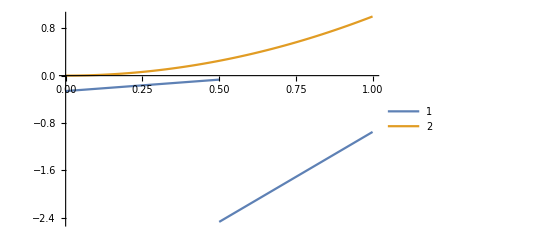

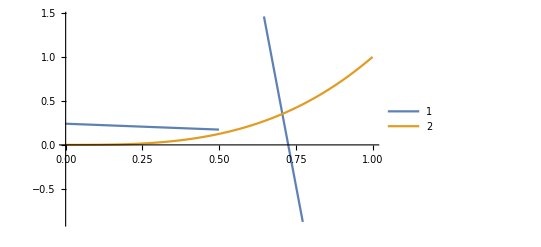

```mathematica
Plot[{ytt[t]⟦1⟧,yReal[t]⟦1⟧},{t,0,1},PlotLegends->Automatic]
Plot[{ytt[t]⟦2⟧,yReal[t]⟦2⟧},{t,0,1},PlotLegends->Automatic]
```

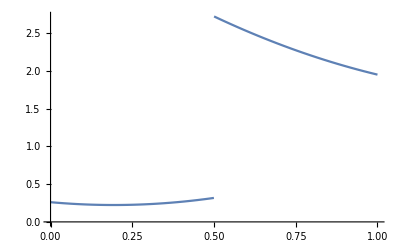

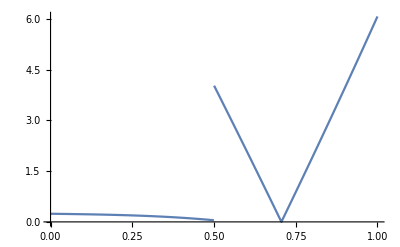

```mathematica
Plot[{Abs[yt[t]⟦1⟧-yReal[t]⟦1⟧]},{t,0,1},PlotLegends->Automatic]
Plot[{Abs[yt[t]⟦2⟧-yReal[t]⟦2⟧]},{t,0,1},PlotLegends->Automatic]
```